```mathematica
V0=1;Δ=1;
```

```mathematica
v1[x_]:=(Sign[x]+1)/2.0 - (Sign[x-π/Δ]+1) +(Sign[x-2*π/Δ]+1)/2.0
```

```mathematica
v2[x_]:=(((Sign[x]+1)/2.0) -((Sign[x-2.0*π/Δ]+1)/2.0))*Sin[Δ*x]
```

```mathematica
v3[x_]:=(((Sign[x]+1)/2.0) -((Sign[x-π/Δ]+1)/2.0))*(x/π)+(((Sign[x-π/Δ]+1)/2.0)-((Sign[x-2*π/Δ]+1.0)/2.0))*((2*π-x)/π)
```

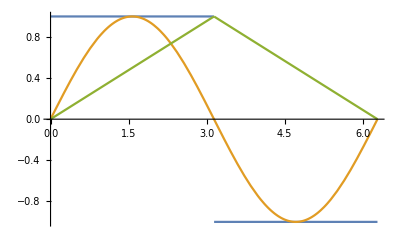

```mathematica
Plot[{v1[x],v2[x],v3[x]},{x,0,2*π},PlotRange->All]
```

```mathematica
c1[t_]:=Integrate[v1[x]*Exp[ⅈ*Δ*x],{x,0,t},Assumptions->{t>0,x>0}]
```

```mathematica
c11[t_]=c1[t]*Conjugate[c1[t]]
```

Conjugate[Piecewise[{{0.+4. ⅈ, t>6.28319}, {(0.+1. ⅈ) (3.+ⅇ^((0.+1. ⅈ) t)), 3.14159<t≤6.28319}, {(0.-1. ⅈ) (-1.+Cos[t]+(0.+1. ⅈ) Sin[t]), True}}]] (Piecewise[{{0.+4. ⅈ, t>6.28319}, {(0.+1. ⅈ) (3.+ⅇ^((0.+1. ⅈ) t)), 3.14159<t≤6.28319}, {(0.-1. ⅈ) (-1.+Cos[t]+(0.+1. ⅈ) Sin[t]), True}}])

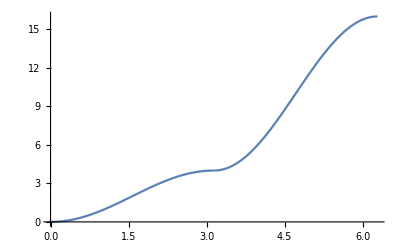

```mathematica
Plot[c11[t],{t,0,2*π}]
```

```mathematica
c2[t_]:=Integrate[Sin [1*x]*Exp[ⅈ*Δ*x],{x,0,t},Assumptions->{t>0,x>0}]
```

```mathematica
c22[t_]=c2[t]*Conjugate[c2[t]]
Δ
```

1/16 (1-ⅇ^(2 ⅈ t)+2 ⅈ t) (1-ⅇ^(-2 ⅈ Conjugate[t])-2 ⅈ Conjugate[t])

1

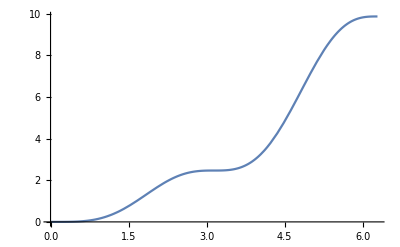

```mathematica
Plot[c22[t],{t,0,2*π}]
```

```mathematica
c3[t_]:=Integrate[v3[x]*Exp[ⅈ*Δ*x],{x,0,t},Assumptions->{t>0,x>0}]
```

```mathematica
c33[t_]=c3[t]*Conjugate[c3[t]]
```

Conjugate[Piecewise[{{-1.27324, t>6.28319}, {(0.-0.31831 ⅈ) ((0.-3. ⅈ)+(6.28319-1. ⅈ) ⅇ^((0.+1. ⅈ) t)-1. ⅇ^((0.+1. ⅈ) t) t), 3.14159<t≤6.28319}, {0.31831 (-1.+Cos[t]-(0.+1. ⅈ) t Cos[t]+(0.+1. ⅈ) Sin[t]+t Sin[t]), True}}]] (Piecewise[{{-1.27324, t>6.28319}, {(0.-0.31831 ⅈ) ((0.-3. ⅈ)+(6.28319-1. ⅈ) ⅇ^((0.+1. ⅈ) t)-1. ⅇ^((0.+1. ⅈ) t) t), 3.14159<t≤6.28319}, {0.31831 (-1.+Cos[t]-(0.+1. ⅈ) t Cos[t]+(0.+1. ⅈ) Sin[t]+t Sin[t]), True}}])

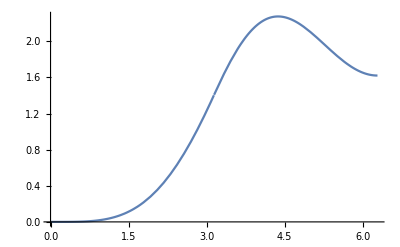

```mathematica
Plot[c33[t],{t,0,2*π}]
```